```mathematica
Quit[]
```

```mathematica
CCxy={{Cxx,Cxy},{Cxy,Cyy}};
CC24={{C22,C24},{C24,C44}};
Ccross={{Cx2,Cx4},{Cy2,Cy4}};
```

```mathematica
meanx=Collect[Collect[Simplify[Simplify[((Ccross.Inverse[CC24].{μ2,-μ2 k3^2})[[1]])/(σ0 ν2 γ1)(1-γ3^2)/.{Cx2->σ1^2 ψ1,Cx4->-σ2^2 ψ2,C22->σ2^2,C24->-σ3^2,C44->σ4^2}]/.{μ2->ν2 σ2,k3^2->σ4/σ2 k3t^2}]/.{σ4->σ3^2/(γ3 σ2),γ1->σ1^2/(σ0 σ2)},{ψ1,ψ2},Simplify]/.{σ1^2->γ1 σ0 σ2},{ψ1,ψ2},Simplify]/.{σ2^4->γ2^2 σ1^2 σ3^2}
```

(1-k3t^2 γ3) ψ1-γ2^2 γ3 (-k3t^2+γ3) ψ2

```mathematica
Varxy=Simplify[CCxy-Ccross.Inverse[CC24].Transpose[Ccross]]/.{Cx2->σ1^2 ψ1x,Cx4->-σ2^2 ψ2x,C22->σ2^2,C24->-σ3^2,C44->σ4^2,Cxx->σ0^2,Cxy->σ0^2 ψ0r,Cyy->σ0^2,Cy2->σ1^2 ψ1y,Cy4->-σ2^2 ψ2y}//Simplify
```

{{(σ0^2 (σ3^4-σ2^2 σ4^2)+σ1^4 σ4^2 ψ1x^2-2 σ1^2 σ2^2 σ3^2 ψ1x ψ2x+σ2^6 ψ2x^2)/(σ3^4-σ2^2 σ4^2),(σ0^2 (σ3^4-σ2^2 σ4^2) ψ0r+σ1^4 σ4^2 ψ1x ψ1y+σ2^6 ψ2x ψ2y-σ1^2 σ2^2 σ3^2 (ψ1y ψ2x+ψ1x ψ2y))/(σ3^4-σ2^2 σ4^2)},{(σ0^2 (σ3^4-σ2^2 σ4^2) ψ0r+σ1^4 σ4^2 ψ1x ψ1y+σ2^6 ψ2x ψ2y-σ1^2 σ2^2 σ3^2 (ψ1y ψ2x+ψ1x ψ2y))/(σ3^4-σ2^2 σ4^2),(σ0^2 (σ3^4-σ2^2 σ4^2)+σ1^4 σ4^2 ψ1y^2-2 σ1^2 σ2^2 σ3^2 ψ1y ψ2y+σ2^6 ψ2y^2)/(σ3^4-σ2^2 σ4^2)}}

```mathematica
Collect[Simplify[Varxy[[1,1]]/σ0^2-1/.{σ3^2->γ3 σ2 σ4,σ3^4->γ3^2 σ2^2 σ4^2,ψ1x->g1ψ1x (σ0 σ2)/σ1^2,ψ2x->g1g2g3ψ2x (σ0 σ4)/σ2^2}]/.{g1ψ1x->γ1 ψ1,g1g2g3ψ2x->γ1 γ2^2 γ3 ψ2},{ψ1,ψ2}]
```

(γ1^2 ψ1^2)/(-1+γ3^2)-(2 γ1^2 γ2^2 γ3^2 ψ1 ψ2)/(-1+γ3^2)+(γ1^2 γ2^4 γ3^2 ψ2^2)/(-1+γ3^2)

```mathematica
γ1 γ2^2 γ3/.{γ1->σ1^2/(σ0 σ2),γ2^2->σ2^4/(σ1^2 σ3^2),γ3->σ3^2/(σ2 σ4)}
```

σ2^2/(σ0 σ4)

```mathematica
Collect[Simplify[(Varxy[[1,2]]/σ0^2-ψ0r)(1-γ3^2)/γ1^2/.{σ3^2->γ3 σ2 σ4,σ3^4->γ3^2 σ2^2 σ4^2,ψ1x->g1ψ1x (σ0 σ2)/σ1^2,ψ2x->g1g2g3ψ2x (σ0 σ4)/σ2^2,ψ1y->g1ψ1y (σ0 σ2)/σ1^2,ψ2y->g1g2g3ψ2y (σ0 σ4)/σ2^2}]/.{g1ψ1x->γ1 ψ1x,g1g2g3ψ2x->γ1 γ2^2 γ3 ψ2x,g1ψ1y->γ1 ψ1y,g1g2g3ψ2y->γ1 γ2^2 γ3 ψ2y},{ψ1x ψ1y,ψ1x ψ2y,ψ2x ψ2y}]
```

-ψ1x ψ1y+γ2^2 γ3^2 ψ1y ψ2x+γ2^2 γ3^2 ψ1x ψ2y-γ2^4 γ3^2 ψ2x ψ2y

## Monochromatic

```mathematica
Quit[]
```

```mathematica
CCxy={{Cxx,Cxy},{Cxy,Cyy}};
Ccross={{Cx2},{Cy2}};
```

```mathematica
meanx[r_]=(Ccross 1/σ2^2 μ2)[[1,1]]/.{Cx2->As ks^2 Sinc[ks r],1/σ2^2->1/(As ks^4)}
```

(μ2 Sinc[ks r])/ks^2

```mathematica
Varxy[x_,y_,r_]=Simplify[CCxy-1/σ2^2 Ccross.Transpose[Ccross]/.{Cxx->As,Cyy->As,Cx2->As ks^2 Sinc[ks x],Cy2->As ks^2 Sinc[ks y],Cxy->As Sinc[ks r],1/σ2^2->1/(As ks^4)}]
```

{{As-As Sinc[ks x]^2,As (Sinc[ks r]-Sinc[ks x] Sinc[ks y])},{As (Sinc[ks r]-Sinc[ks x] Sinc[ks y]),As-As Sinc[ks y]^2}}

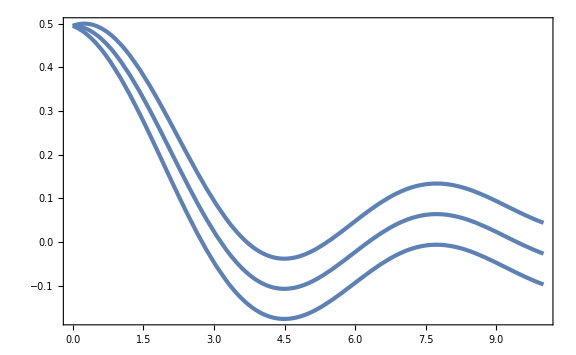

```mathematica
Plot[{meanx[r],meanx[r]+Sqrt[Varxy[r,r,0][[1,1]]],meanx[r]-Sqrt[Varxy[r,r,0][[1,1]]]}/.{μ2->7Sqrt[5 10^-3],ks->1,As->5 10^-3},{r,0,10}]
```

```mathematica
tpf[x_,y_,r_]=Varxy[x,y,r][[1,2]]+meanx[x]meanx[y]
```

(μ2^2 Sinc[ks x] Sinc[ks y])/ks^4+As (Sinc[ks r]-Sinc[ks x] Sinc[ks y])

```mathematica
WRTH[z_]=3(Sin[z]-z Cos[z])/z^3;
```

```mathematica
ks r Sinc'[ks r]+(ks r)^2/3 WRTH[ks r]//Simplify
```

0

```mathematica
Sinc'[z]+z/3 WRTH[z]//Simplify
```

0

```mathematica
WRTH'[z]//Expand
```

(9 Cos[z])/z^3-(9 Sin[z])/z^4+(3 Sin[z])/z^2

```mathematica
WRTH[z]^2//Expand
```

(9 Cos[z]^2)/z^4-(18 Cos[z] Sin[z])/z^5+(9 Sin[z]^2)/z^6

## Lognormal

```mathematica
Quit[]
```

```mathematica
s2s=10^-1;
As=3.5 10^-3;
npeak=16;
nbias=16;
NL=256;
kpeak=(2π npeak)/NL
```

π/8

```mathematica
WRTH[z_]=3(Sin[z]-z Cos[z])/z^3;
```

```mathematica
calPz[lnk_,s2_]=Ag/Sqrt[2π s2] Exp[-lnk^2/(2s2)];
```

```mathematica
σn2[n_,s2_]=Ag E^(2 n^2 s2)ks^(2n);
```

```mathematica
γn[s2_]=Simplify[σn2[n,s2]/Sqrt[σn2[n-1,s2]σn2[n+1,s2]],{ks>0,n>0,s2>0,Ag>0}]
```

ⅇ^(-2 s2)

```mathematica
ψn[x_,n_,s2_]:=NIntegrate[Simplify[ks^(2n)/σn2[n,s2] E^(2n lnk)calPz[lnk,s2]Sinc[E^lnk x]],{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[ψ1List=ParallelTable[{x,ψn[x,1,s2s]},{x,10^-2,10,10^-2}];
ψ2List=ParallelTable[{x,ψn[x,2,s2s]},{x,10^-2,10,10^-2}];]
```

{8.40184,Null}

```mathematica
ψ1int[x_]=Interpolation[ψ1List][x];
ψ2int[x_]=Interpolation[ψ2List][x];
```

```mathematica
Deltaζ[x_]=Sqrt[σn2[0,s2s](1-γn[s2s]^2/(1-γn[s2s]^2)(ψ1int[x]^2-2 γn[s2s]^4 ψ1int[x]ψ2int[x]+γn[s2s]^6 ψ2int[x]^2))/.{Ag->As}];
```

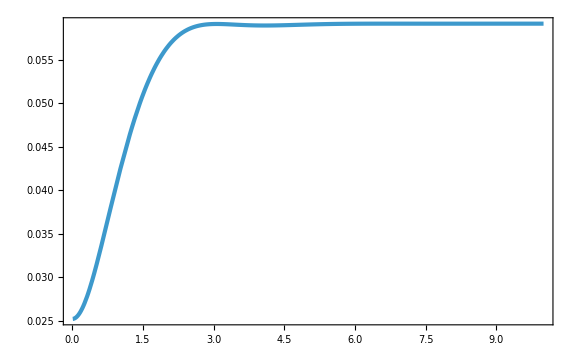

```mathematica
Plot[Deltaζ[x],{x,0.01,10},PlotRange->Full]
```

```mathematica
ψnr[x_,n_,s2_]:=NIntegrate[ks^(2n)/σn2[n,s2] E^(2n lnk)calPz[lnk,s2]WRTH[E^lnk x]//Simplify,{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
ψnrr[x_,n_,s2_]:=NIntegrate[ks^(2n)/σn2[n,s2] E^(2n lnk)calPz[lnk,s2] WRTH[E^lnk x]^2//Simplify,{lnk,-∞,∞},Method->"GaussKronrodRule",WorkingPrecision->30]
```

```mathematica
AbsoluteTiming[ψ1rList=ParallelTable[{x,ψnr[x,1,s2s]},{x,10^-2,10,10^-2}];
ψ2rList=ParallelTable[{x,ψnr[x,2,s2s]},{x,10^-2,10,10^-2}];
ψ1rrList=ParallelTable[{x,ψnrr[x,1,s2s]},{x,10^-2,10,10^-2}];]
```

{29.7986,Null}

```mathematica
ψ1rint[x_]=Interpolation[ψ1rList][x];
ψ2rint[x_]=Interpolation[ψ2rList][x];
ψ1rrint[x_]=Interpolation[ψ1rrList][x];
```

```mathematica
DeltaC[x_]=-2 σn2[0,s2s]/27(σn2[2,s2s]/σn2[0,s2s] x^4/ks^4 ψ1rrint[x]-γn[s2s]^2/(1-γn[s2s]^2)(σn2[2,s2s]^2/σn2[1,s2s]^2 x^4/ks^4 ψ1rint[x]^2-2 γn[s2s]^4 σn2[3,s2s]/σn2[1,s2s] x^4/ks^4 ψ1rint[x]ψ2rint[x]+γn[s2s]^6 σn2[3,s2s]^2/σn2[2,s2s]^2 x^4/ks^4 ψ2rint[x]^2))/.{Ag->As};
```

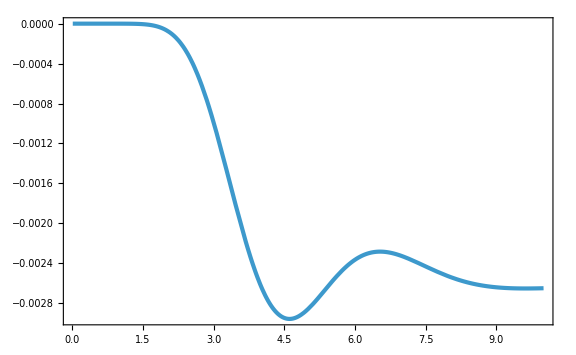

```mathematica
Plot[DeltaC[x],{x,0.01,10}]
```